```mathematica
(*Basado en el uso de la función de Heun en https://arxiv.org/pdf/2206.07721.pdf*)
```

```mathematica
(*Parámetros*)
Clear[M,L,μ,l,m1,m2]
M=5;
L=1;
μ=0.01;
l=2;
m1=1;
m2=1;
```

```mathematica
Delta[r_]:=(1/r^2)(r^2+a1^2)(r^2+a2^2)(1+(r^2/L^2))-2*M;
Simplify[(r/.Solve[Delta[r]==0,r][[1]])^2]==Simplify[(r/.Solve[Delta[r]==0,r][[2]])^2]
Simplify[(r/.Solve[Delta[r]==0,r][[3]])^2]==Simplify[(r/.Solve[Delta[r]==0,r][[4]])^2]
Simplify[(r/.Solve[Delta[r]==0,r][[5]])^2]==Simplify[(r/.Solve[Delta[r]==0,r][[6]])^2]
```

True

True

True

```mathematica
Simplify[(r/.Solve[Delta[r]==0,r][[1]])^2]/.{a1->.1,a2->.1,M->5.,L->1.}
Simplify[(r/.Solve[Delta[r]==0,r][[3]])^2]/.{a1->.1,a2->.1,M->5.,L->1.}
Simplify[(r/.Solve[Delta[r]==0,r][[5]])^2]/.{a1->.1,a2->.1,M->5.,L->1.}
```

2.68999-8.88178×10^-16 ⅈ

0.0000100202+1.37906×10^-15 ⅈ

-3.71-8.88178×10^-16 ⅈ

```mathematica
Clear[r0,rmenos,rmas]
r0[a3_,a4_]:=Simplify[(r/.Solve[Delta[r]==0,r][[6]])/.{a1->a3,a2->a4}];
rmenos[a3_,a4_]:=Simplify[(r/.Solve[Delta[r]==0,r][[4]])/.{a1->a3,a2->a4}];
rmas[a3_,a4_]:=Simplify[(r/.Solve[Delta[r]==0,r][[2]])/.{a1->a3,a2->a4}];
Z0[a1_,a2_]:=(rmenos[a1,a2]^2-rmas[a1,a2]^2)/(rmenos[a1,a2]^2-r0[a1,a2]^2);
σ=2+Sqrt[4+μ^2*L^2];
Ξ1[a1_,a2_]:=1-(a1^2/L^2);
Ξ2[a1_,a2_]:=1-(a2^2/L^2);
Ω01[a1_,a2_]:=(a1*Ξ1[a1,a2])/(r0[a1,a2]^2+a1^2);
Ω02[a1_,a2_]:=(a2*Ξ2[a1,a2])/(r0[a1,a2]^2+a2^2);
Ωmenos1[a1_,a2_]:=(a1*Ξ1[a1,a2])/(rmenos[a1,a2]^2+a1^2);
Ωmenos2[a1_,a2_]:=(a2*Ξ2[a1,a2])/(rmenos[a1,a2]^2+a2^2);
Ωmas1[a1_,a2_]:=(a1*Ξ1[a1,a2])/(rmas[a1,a2]^2+a1^2);
Ωmas2[a1_,a2_]:=(a2*Ξ2[a1,a2])/(rmas[a1,a2]^2+a2^2);
T0[a1_,a2_]:=(r0[a1,a2](r0[a1,a2]^2-rmenos[a1,a2]^2)(r0[a1,a2]^2-rmas[a1,a2]^2))/(2*Pi*L^2*(r0[a1,a2]^2+a1^2)(r0[a1,a2]^2+a2^2));
Tmenos[a1_,a2_]:=(rmenos[a1,a2](rmenos[a1,a2]^2-r0[a1,a2]^2)(rmenos[a1,a2]^2-rmas[a1,a2]^2))/(2*Pi*L^2*(rmenos[a1,a2]^2+a1^2)(rmenos[a1,a2]^2+a2^2));
Tmas[a1_,a2_]:=(rmas[a1,a2](rmas[a1,a2]^2-rmenos[a1,a2]^2)(rmas[a1,a2]^2-r0[a1,a2]^2))/(2*Pi*L^2*(rmas[a1,a2]^2+a1^2)(rmas[a1,a2]^2+a2^2));
θ0[a1_,a2_,ω_]:=(I(ω-m1*Ω01[a1,a2]-m2*Ω02[a1,a2]))/(2*Pi*T0[a1,a2]);
θmenos[a1_,a2_,ω_]:=(I(ω-m1*Ωmenos1[a1,a2]-m2*Ωmenos2[a1,a2]))/(2*Pi*Tmenos[a1,a2]);
θmas[a1_,a2_,ω_]:=(I(ω-m1*Ωmas1[a1,a2]-m2*Ωmas2[a1,a2]))/(2*Pi*Tmas[a1,a2]);
(*Sólo para a1=a2*)
λ[a1_,a2_,ω_]:=Ξ1[a1,a2]*(l(l+2)-2*ω*a1*(m1+m2)-(a1^2/L^2)*(m1+m2)^2)+a1^2*(ω^2+μ^2);
qr[a1_,a2_,ω_]:=(1/4)*(((ω^2*L^2-λ[a1,a2,ω]-rmas[a1,a2]*μ^2)/(rmenos[a1,a2]^2-r0[a1,a2]^2))*L^2+2*Z0[a1,a2](σ*θmas[a1,a2,ω]+σ-θmas[a1,a2,ω])+(θmas[a1,a2,ω]+θmenos[a1,a2,ω])*(θmas[a1,a2,ω]+θmenos[a1,a2,ω]+2)-θ0[a1,a2,ω]^2);
αr[a1_,a2_,ω_]:=(1/2)(σ+θmas[a1,a2,ω]+θmenos[a1,a2,ω]+θ0[a1,a2,ω]);
βr[a1_,a2_,ω_]:=(1/2)(σ+θmas[a1,a2,ω]+θmenos[a1,a2,ω]-θ0[a1,a2,ω]);
γr[a1_,a2_,ω_]:=1+θmas[a1,a2,ω];
δr=-1+σ;
ϵr[a1_,a2_,ω_]:=1+θmenos[a1,a2,ω];
```

```mathematica
αr[.1,.1,1]
βr[.1,.1,1]
γr[.1,.1,1]
δr
ϵr[.1,.1,1]
γr[.1,.1,1]+δr+ϵr[.1,.1,1]-αr[.1,.1,1]-βr[.1,.1,1]-1
```

1.84233+0.149406 ⅈ

2.15769+0.149406 ⅈ

1.+0.239246 ⅈ

3.00002

1.+0.0595672 ⅈ

0.+0. ⅈ

```mathematica
y01[a1_,a2_,ω_,z_]:=HeunG[Z0[a1,a2],qr[a1,a2,ω],αr[a1,a2,ω],βr[a1,a2,ω],γr[a1,a2,ω],δr,z];
y02[a1_,a2_,ω_,z_]:=(z^(1-γr[a1,a2,ω]))HeunG[Z0[a1,a2],(Z0[a1,a2]*δr+ϵr[a1,a2,ω])*(1-γr[a1,a2,ω])+qr[a1,a2,ω],αr[a1,a2,ω]+1-γr[a1,a2,ω],βr[a1,a2,ω]+1-γr[a1,a2,ω],2-γr[a1,a2,ω],δr,z];
y11[a1_,a2_,ω_,z_]:=HeunG[1-Z0[a1,a2],αr[a1,a2,ω]*βr[a1,a2,ω]-qr[a1,a2,ω],αr[a1,a2,ω],βr[a1,a2,ω],δr,γr[a1,a2,ω],1-z];
y12[a1_,a2_,ω_,z_]:=((1-z)^(1-δr))HeunG[1-Z0[a1,a2],((1-Z0[a1,a2])*γr[a1,a2,ω]+ϵr[a1,a2,ω])*(1-δr)+αr[a1,a2,ω]*βr[a1,a2,ω]-qr[a1,a2,ω],αr[a1,a2,ω]+1-δr,βr[a1,a2,ω]+1-δr,2-δr,γr[a1,a2,ω],1-z];
```

```mathematica
y01[.1,.1,1,.5]
y02[.1,.1,1,.5]
y11[.1,.1,1,.5]
y12[.1,.1,1,.5]
```

4.88364-0.767091 ⅈ

4.73654+1.41546 ⅈ

2.06397+0.192734 ⅈ

2304.17+215.164 ⅈ

```mathematica
C22[a1_,a2_,ω_]:=(Wronskian[{y02[a1,a2,ω,z],y11[a1,a2,ω,z]},z]/Wronskian[{y12[a1,a2,ω,z],y11[a1,a2,ω,z]},z])/.{z->.2}
```

```mathematica
tabl={0.05,0.1,0.15,0.2,0.25,0.3,0.35}
Table[ω[tabl[[i]],2]=ω/.FindRoot[C22[tabl[[i]],tabl[[i]],ω]==0,{ω,7-4*I}],{i,1,7,1}]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35}

{6.87206-4.0541 ⅈ,6.72489-4.03239 ⅈ,6.58505-4.04282 ⅈ,6.45069-4.08937 ⅈ,6.31993-4.17871 ⅈ,6.1908-4.32197 ⅈ,6.0617-4.53871 ⅈ}

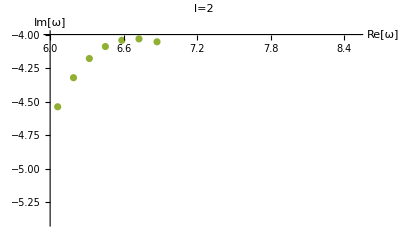

```mathematica
ListPlot[{Table[{Re[ω[tabl[[i]]]],Im[ω[tabl[[i]]]]},{i,1,7,1}],Table[{Re[ω[tabl[[i]],-2]],Im[ω[tabl[[i]],-2]]},{i,1,7,1}],Table[{Re[ω[tabl[[i]],2]],Im[ω[tabl[[i]],2]]},{i,1,7,1}]},PlotRange-> {{6,8.5},{-4,-5.4}},AxesLabel->{"Re[ω]","Im[ω]"},PlotLabel->"l=2",LabelStyle->Bold, AxesStyle->Thick]
```

```mathematica
ω1[0]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0.001-1.9*I}]
```

0.00027553-1.71536 ⅈ

```mathematica
ω1[1]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0-2*I}]
ω1[2]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0-4*I}]
ω1[3]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0-5*I}]
ω1[4]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0-7*I}]
ω1[5]=ω/.FindRoot[C22[0.9999,0.9999,ω]==0,{ω,0-8*I}]
```

0.00027553-1.71536 ⅈ

0.000298691-3.32718 ⅈ

0.00031585-4.89894 ⅈ

0.000329264-6.45433 ⅈ

0.00034042-8.00412 ⅈ

```mathematica
sr=m1*Ωmas1[0.9999,0.9999]+m2*Ωmas2[0.9999,0.9999]
line1=Line[{{Re[sr],0},{Re[sr],-9}}];
lineStyle={Thick,Red,Dashed};
```

0.00016501+7.55851×10^-20 ⅈ

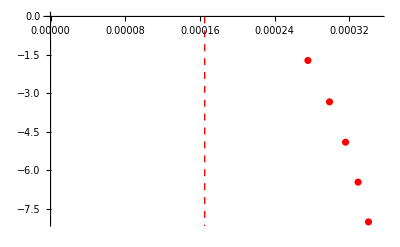

```mathematica
ListPlot[{{0.00027552961283257955,-1.7153609584396399},{0.0002986909691694507,-3.3271846345795333 },{0.0003158496198322996,-4.898937112101537},{0.0003292635801658726,-6.454325059965198},{0.00034041997822945274,-8.004116464762978}},PlotRange->{{0,0.00035},Automatic},PlotStyle->{Automatic,Directive[lineStyle],Directive[lineStyle]},Epilog->{Directive[lineStyle],line1}](*m1+m2=2*)
```